# Coordinate mapping

Work in progress

```mathematica
PeS=PowerExpand[Simplify[##]]&
FpPeS=FixedPoint[PeS,##]&
```

PowerExpand[Simplify[##1]]&

FixedPoint[PeS,##1]&

```mathematica
FsSubst[rules_]:=FullSimplify[#//.rules]&
FpFsSubst[rules_]:=FixedPoint[FsSubst[rules],#]&
```

```mathematica
LSolve=Last[Solve[##]]&
```

Last[Solve[##1]]&

## Coordinate transformation for the muralizer

We want to map Cartesian coordinates x⃗≡(x
y) into radii (r_A
r_B) from two reference points, A⃗≡(x_A
y_A),B⃗≡(x_B
y_B).

(r_A
r_B)=(√((x-x_A)^2+(y-y_A)^2)
√((x-x_B)^2+(y-y_B)^2))=√(⟨x⃗-A⃗|x⃗-A⃗⟩
⟨x⃗-B⃗|x⃗-B⃗⟩)

```mathematica
stringcoordinates[refpoints_]:=Function[{x},√(#.#)&[x-#]&/@refpoints]
```

```mathematica
refpoints={{-1/2,0},{1/2,0}}
```

{{-1/2,0},{1/2,0}}

```mathematica
stringcoordinates[refpoints][{x,y}]
```

{√((1/2+x)^2+y^2),√((-1/2+x)^2+y^2)}

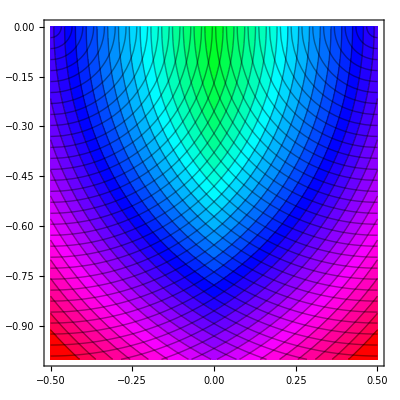

```mathematica
ContourPlot[stringcoordinates[refpoints][{x,y}],{x,-1/2,1/2},{y,-1,0},ColorFunction->Hue,Contours->41]
```

### Transformation of a straight line

#### Examples

```mathematica
refpoints
```

{{-1/2,0},{1/2,0}}

```mathematica
TableForm[lineset={
{{-0.5,0},{0.5,0}},
{{0,0},{0,-1}},
{{-0.5,-0.5},{0.5,-0.5}},
{{-0.5,0},{-0.5,-1}},
{{0.5,0},{0.5,-1}},
{{-0.5,-1},{0.5,-1}},
{{-0.5,0},{0.5,-1}},
{{0.5,0},{-0.5,-1}},
{{-0.5,-0.5},{0,0}},
{{0.5,-0.5},{0,0}},
{{-0.5,-0.5},{0,-1}},
{{0.5,-0.5},{0,-1}}
},TableDepth->2]
```

{-0.5,0} | {0.5,0}
{0,0} | {0,-1}
{-0.5,-0.5} | {0.5,-0.5}
{-0.5,0} | {-0.5,-1}
{0.5,0} | {0.5,-1}
{-0.5,-1} | {0.5,-1}
{-0.5,0} | {0.5,-1}
{0.5,0} | {-0.5,-1}
{-0.5,-0.5} | {0,0}
{0.5,-0.5} | {0,0}
{-0.5,-0.5} | {0,-1}
{0.5,-0.5} | {0,-1}

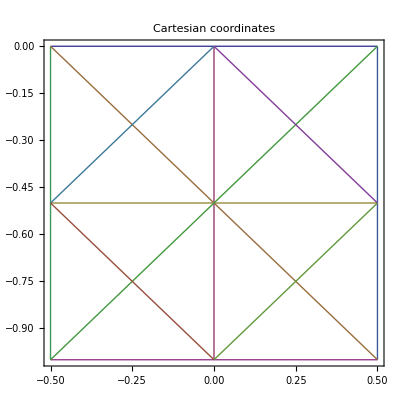

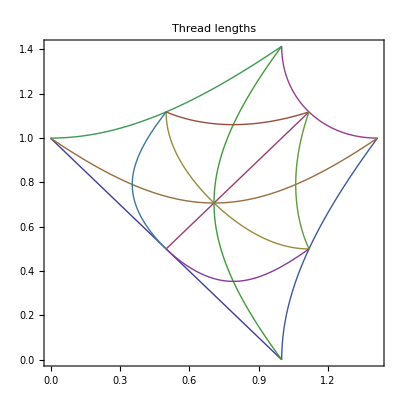

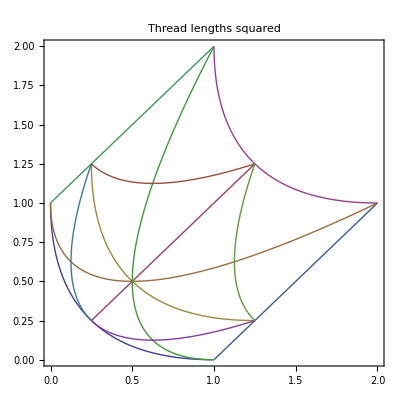

```mathematica
Print/@{
ParametricPlot[Evaluate[#⟦1⟧(1-t)+#⟦2⟧t&/@#],{t,0,1},PlotRange->All,Frame->True,Axes->False,PlotLabel->"Cartesian coordinates"]&[lineset],ParametricPlot[Evaluate[stringcoordinates[refpoints][#⟦1⟧(1-t)+#⟦2⟧t]&/@#],{t,0,1},PlotRange->All,Frame->True,PlotLabel->"Thread lengths"]&[lineset],ParametricPlot[Evaluate[(stringcoordinates[refpoints][#⟦1⟧(1-t)+#⟦2⟧t])^2&/@#],{t,0,1},PlotRange->All,Frame->True,PlotLabel->"Thread lengths squared"]&[lineset]
};
```

#### Mathematics

```mathematica
Simplify[{x1,y1}(1-t)+{x2,y2}t/.{x1->x-δx/2,y1->y-δy/2,x2->x+δx/2,y2->y+δy/2}]
```

{x+(-1/2+t) δx,y+(-1/2+t) δy}

as implicit function: a quadratic form in {R,S}

```mathematica
{R,S}==FullSimplify[{#.#&[{Xx,Yy}-{XA,YA}],#.#&[{Xx,Yy}-{XB,YB}]}/.{XA->X0-ΔX/2,YA->Y0-ΔY/2,XB->X0+ΔX/2,YB->Y0+ΔY/2}/.{Xx->x+(t-1/2)δx,Yy->y+(t-1/2)δy}]
Eliminate[%,t]/.{(A_==B_)->(A-B==0)}
Collect[First[%],{R,S},Simplify]
TableForm[coefficients=FullSimplify[LSolve[%==a R^2+b S^2+c R S+d R+e S+f/.{{R->0,S->0},{R->1,S->0},{R->1,S->1},{R->0,S->1},{R->-1,S->-1},{R->0,S->-1},{R->-1,S->0},{R->200,S->-42}},{a,b,c,d,e,f}]]
]
```

{R,S}=={(x-X0+(-1/2+t) δx+ΔX/2)^2+(y-Y0+(-1/2+t) δy+ΔY/2)^2,1/4 ((-2 x+2 X0+δx-2 t δx+ΔX)^2+(-2 y+2 Y0+δy-2 t δy+ΔY)^2)}

S^2 δx^2-2 S δx^2 ΔX^2+4 y^2 δx^2 ΔX^2-8 y Y0 δx^2 ΔX^2+4 Y0^2 δx^2 ΔX^2+δx^2 ΔX^4-4 S y δx ΔX δy+4 S Y0 δx ΔX δy-8 x y δx ΔX^2 δy+8 X0 y δx ΔX^2 δy+8 x Y0 δx ΔX^2 δy-8 X0 Y0 δx ΔX^2 δy+S^2 δy^2+4 S x ΔX δy^2-4 S X0 ΔX δy^2+4 x^2 ΔX^2 δy^2-8 x X0 ΔX^2 δy^2+4 X0^2 ΔX^2 δy^2+R^2 (δx^2+δy^2)+4 S y δx^2 ΔY-4 S Y0 δx^2 ΔY-4 S x δx δy ΔY+4 S X0 δx δy ΔY-4 S δx ΔX δy ΔY+2 δx ΔX^3 δy ΔY+4 y^2 δx^2 ΔY^2-8 y Y0 δx^2 ΔY^2+4 Y0^2 δx^2 ΔY^2+δx^2 ΔX^2 ΔY^2-8 x y δx δy ΔY^2+8 X0 y δx δy ΔY^2+8 x Y0 δx δy ΔY^2-8 X0 Y0 δx δy ΔY^2-2 S δy^2 ΔY^2+4 x^2 δy^2 ΔY^2-8 x X0 δy^2 ΔY^2+4 X0^2 δy^2 ΔY^2+ΔX^2 δy^2 ΔY^2+2 δx ΔX δy ΔY^3+δy^2 ΔY^4+R (-2 S δx^2-2 δx^2 ΔX^2+4 y δx ΔX δy-4 Y0 δx ΔX δy-2 S δy^2-4 x ΔX δy^2+4 X0 ΔX δy^2-4 y δx^2 ΔY+4 Y0 δx^2 ΔY+4 x δx δy ΔY-4 X0 δx δy ΔY-4 δx ΔX δy ΔY-2 δy^2 ΔY^2)==0

R^2 (δx^2+δy^2)+S^2 (δx^2+δy^2)+(ΔX^2+ΔY^2) (4 y^2 δx^2+4 Y0^2 δx^2+δx^2 ΔX^2+8 (x-X0) Y0 δx δy+4 x^2 δy^2-8 x X0 δy^2+4 X0^2 δy^2-8 y δx (Y0 δx+(x-X0) δy)+2 δx ΔX δy ΔY+δy^2 ΔY^2)-2 S (δx^2 (ΔX^2+2 (-y+Y0) ΔY)+2 δx δy (y ΔX-Y0 ΔX+(x-X0+ΔX) ΔY)+δy^2 (-2 x ΔX+2 X0 ΔX+ΔY^2))+R (-2 S (δx^2+δy^2)-2 (δx^2 (ΔX^2+2 (y-Y0) ΔY)+2 δx δy (-y ΔX+Y0 ΔX+(-x+X0+ΔX) ΔY)+δy^2 (2 x ΔX-2 X0 ΔX+ΔY^2)))

a→δx^2+δy^2
b→δx^2+δy^2
c→-2 (δx^2+δy^2)
d→-2 (δx^2 (ΔX^2+2 (y-Y0) ΔY)+2 δx δy (-y ΔX+Y0 ΔX+(-x+X0+ΔX) ΔY)+δy^2 (2 x ΔX-2 X0 ΔX+ΔY^2))
e→-2 (δx^2 (ΔX^2+2 (-y+Y0) ΔY)+2 δx δy (y ΔX-Y0 ΔX+(x-X0+ΔX) ΔY)+δy^2 (-2 x ΔX+2 X0 ΔX+ΔY^2))
f→(ΔX^2+ΔY^2) (4 y^2 δx^2+4 Y0^2 δx^2+8 (x-X0) Y0 δx δy+4 (x-X0)^2 δy^2-8 y δx (Y0 δx+(x-X0) δy)+(δx ΔX+δy ΔY)^2)

```mathematica
TableForm[FpFsSubst[{δx^2+δy^2->δ^2,ΔX^2+ΔY^2->Δ^2,x->X0+ξ,y->Y0+υ}][coefficients]]
Simplify[{(d+e)/2,(d-e)/2}/.%]
```

a→δ^2
b→δ^2
c→-2 δ^2
d→-2 (δy^2 (ΔY^2+2 ΔX ξ)+δx^2 (ΔX^2+2 ΔY υ)-2 δx δy (ΔY ξ+ΔX (-ΔY+υ)))
e→-2 (δy^2 (ΔY^2-2 ΔX ξ)+δx^2 (ΔX^2-2 ΔY υ)+2 δx δy (ΔY ξ+ΔX (ΔY+υ)))
f→Δ^2 (δy^2 (ΔY^2+4 ξ^2)+2 δx δy (ΔX ΔY-4 ξ υ)+δx^2 (ΔX^2+4 υ^2))

{-2 (δx ΔX+δy ΔY)^2,-4 (ΔX δy-δx ΔY) (δy ξ-δx υ)}

```mathematica
TableForm[({a,b,c,d,e,f}/.coefficients)]
```

δx^2+δy^2
δx^2+δy^2
-2 (δx^2+δy^2)
-2 (δx^2 (ΔX^2+2 (y-Y0) ΔY)+2 δx δy (-y ΔX+Y0 ΔX+(-x+X0+ΔX) ΔY)+δy^2 (2 x ΔX-2 X0 ΔX+ΔY^2))
-2 (δx^2 (ΔX^2+2 (-y+Y0) ΔY)+2 δx δy (y ΔX-Y0 ΔX+(x-X0+ΔX) ΔY)+δy^2 (-2 x ΔX+2 X0 ΔX+ΔY^2))
(ΔX^2+ΔY^2) (4 y^2 δx^2+4 Y0^2 δx^2+8 (x-X0) Y0 δx δy+4 (x-X0)^2 δy^2-8 y δx (Y0 δx+(x-X0) δy)+(δx ΔX+δy ΔY)^2)

```mathematica
TableForm[Simplify[
{δx^2+δy^2,
δx^2+δy^2,
-2(δx^2+δy^2),
-2 (δx ΔX+δy ΔY)^2-4 (ΔX δy-δx ΔY) (δy (x-X0)-δx (y-Y0)),
-2 (δx ΔX+δy ΔY)^2+4 (ΔX δy-δx ΔY) (δy (x-X0)-δx (y-Y0)),
(ΔX^2+ΔY^2)((δx ΔX+δy ΔY)^2+4(δy (x-X0)-δx (y-Y0))^2)}-({a,b,c,d,e,f}/.coefficients)]]
```

0
0
0
0
0
0

### Implicit equation for thread lengths squared to draw a straight line

To draw a straight line from (x_1
y_1) to (x_2
y_2) in Cartesian coordinates, the thread lengths {r,s} of the spools suspended from the points {(X_a
Y_a),(X_b
Y_b)} follow the implicit equation
(r^2 | s^2)·(A | C
C | B)·(r^2
s^2)+(r^2 | s^2)(D
E)+F==0
with
A≡B≡-C≡δx^2+δy^2
D≡-2 (δx ΔX+δy ΔY)^2-4 (ΔX δy-δx ΔY) (δy (x-X_0)-δx (y-Y_0))
E≡-2 (δx ΔX+δy ΔY)^2+4 (ΔX δy-δx ΔY) (δy (x-X_0)-δx (y-Y_0))
F≡(ΔX^2+ΔY^2)((δx ΔX+δy ΔY)^2+4(δy (x-X_0)-δx (y-Y_0))^2)
where
X_0≡(X_a+X_b)/2,
Y_0≡(Y_a+Y_b)/2,
ΔX≡X_b-X_a,
ΔY≡Y_b-Y_a,
x≡(x_1+x_2)/2,
y≡(y_1+y_2)/2,
δx≡x_2-x_1,
δy≡y_2-y_1.

#### Sanity check

```mathematica
Chop[Simplify[((Function[{r,s},Evaluate[Simplify[{R,S}.{{a,c/2},{c/2,b}}.{R,S}+{R,S}.{d,e}+f/.coefficients/.{ΔX->XB-XA,ΔY->YB-YA,X0->(XA+XB)/2,Y0->(YA+YB)/2,δx->x2-x1,δy->y2-y1,x->(x1+x2)/2,y->(y1+y2)/2}/.{R->r^2,S->s^2}]]
]/.{XA->refpoints⟦1,1⟧,YA->refpoints⟦1,2⟧,XB->refpoints⟦2,1⟧,YB->refpoints⟦2,2⟧}/.{x1->#⟦1,1⟧,y1->#⟦1,2⟧,x2->#⟦2,1⟧,y2->#⟦2,2⟧})@@(stringcoordinates[refpoints][#⟦1⟧(1-t)+#⟦2⟧t]))&/@lineset]]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

#### Sign of derivatives

```mathematica
Print["Discriminant"];{R,S}.(δ^2{{1,-1},{-1,1}}.{R,S}-2(ΔX δx+ΔY δy)^2{1,1}+4(ΔX δy-ΔY δx)(δy(x-X0)-δx(y-Y0)){-1,1})+Δ^2((ΔX δx+ΔY δy)^2+4(δy(x-X0)-δx(y-Y0))^2)
Print["Gradient"];D[%,#]&/@{R,S}
FullSimplify[%//.{δ^2->δx^2+δy^2,ΔX->Xb-Xa,ΔY->Yb-Ya,X0->(Xa+Xb)/2,Y0->(Ya+Yb)/2,δx->x2-x1,δy->y2-y1,x->(x1+x2)/2,y->(y1+y2)/2}]
FullSimplify[%/.{R->(x1-Xa)^2+(y1-Ya)^2,S->(x1-Xb)^2+(y1-Yb)^2}]
Print["Initial direction"];Series[FullSimplify[{R,S}/.{R->(x1+t(x2-x1)-Xa)^2+(y1+t(y2-y1)-Ya)^2,S->(x1+t(x2-x1)-Xb)^2+(y1+t(y2-y1)-Yb)^2}],{t,0,1}]
FullSimplify[#⟦3,2⟧&/@%]
Print["Ratio"];FullSimplify[({{0,1},{1,0}}.%%%)/%]
```

Discriminant

R ((R-S) δ^2-4 (-(y-Y0) δx+(x-X0) δy) (ΔX δy-δx ΔY)-2 (δx ΔX+δy ΔY)^2)+S ((-R+S) δ^2+4 (-(y-Y0) δx+(x-X0) δy) (ΔX δy-δx ΔY)-2 (δx ΔX+δy ΔY)^2)+Δ^2 (4 (-(y-Y0) δx+(x-X0) δy)^2+(δx ΔX+δy ΔY)^2)

Gradient

{R δ^2+(R-S) δ^2-S δ^2-4 (-(y-Y0) δx+(x-X0) δy) (ΔX δy-δx ΔY)-2 (δx ΔX+δy ΔY)^2,-R δ^2+S δ^2+(-R+S) δ^2+4 (-(y-Y0) δx+(x-X0) δy) (ΔX δy-δx ΔY)-2 (δx ΔX+δy ΔY)^2}

{R ((x1-x2)^2+(y1-y2)^2)+(R-S) ((x1-x2)^2+(y1-y2)^2)-S ((x1-x2)^2+(y1-y2)^2)-2 ((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb))^2+2 (-(Xa-Xb) (y1-y2)+(x1-x2) (Ya-Yb)) ((Xa+Xb) (y1-y2)+x1 (2 y2-Ya-Yb)+x2 (-2 y1+Ya+Yb)),-R ((x1-x2)^2+(y1-y2)^2)+S ((x1-x2)^2+(y1-y2)^2)+(-R+S) ((x1-x2)^2+(y1-y2)^2)-2 ((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb))^2+2 ((Xa-Xb) (y1-y2)-(x1-x2) (Ya-Yb)) ((Xa+Xb) (y1-y2)+x1 (2 y2-Ya-Yb)+x2 (-2 y1+Ya+Yb))}

{4 (x1^2+x2 Xb-x1 (x2+Xb)+(y1-y2) (y1-Yb)) (-(x1-x2) (Xa-Xb)-(y1-y2) (Ya-Yb)),4 (x1^2+x2 Xa-x1 (x2+Xa)+(y1-y2) (y1-Ya)) ((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb))}

Initial direction

{((-x1+Xa)^2+(-y1+Ya)^2)+(2 (x1-x2) (-x1+Xa)+2 (y1-y2) (-y1+Ya)) t+O[t]^2,((-x1+Xb)^2+(-y1+Yb)^2)+(2 (x1-x2) (-x1+Xb)+2 (y1-y2) (-y1+Yb)) t+O[t]^2}

{2 (x1-x2) (-x1+Xa)+2 (y1-y2) (-y1+Ya),2 (x1-x2) (-x1+Xb)+2 (y1-y2) (-y1+Yb)}

Ratio

{-2 ((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb)),2 ((x1-x2) (Xa-Xb)+(y1-y2) (Ya-Yb))}

### Inverse transformation

r_A^2==(x-x_A)^2+(y-y_A)^2==x^2-2x x_A+x_A^2+y^2-2y y_A+y_A^2
r_B^2==(x-x_B)^2+(y-y_B)^2==x^2-2x x_B+x_B^2+y^2-2y y_B+y_B^2

```mathematica
FpPeS[Solve[{r,s}==stringcoordinates[{{A,C},{B,D}}][{x,y}],{x,y}]];
FullSimplify[%//.{A^2-2 A B+B^2->(A-B)^2,A^2 C-2 A B C+B^2 C->C(A-B)^2,A^2 D-2 A B D+B^2 D->D(A-B)^2,C^2-2 C D+D^2->(C-D)^2,C^4-4 C^3 D+6 C^2 D^2-4 C D^3+D^4->(C-D)^4,-2 C^2 r^2+4 C D r^2-2 D^2 r^2->-2 (C-D)^2 r^2,-2 C^2 s^2+4 C D s^2-2 D^2 s^2->-2 (C-D)^2 s^2,r^4-2 r^2 s^2+s^4->(r^2-s^2)^2}];
FullSimplify[%//.{A^2 (C+D)-2 A B (C+D)+B^2 (C+D)->(A-B)^2(C+D),(C-D) (C^2-D^2-r^2+s^2)->(C-D)^2(C+D)-(C-D)(r^2-s^2),(A-B)^2 (C+D)+(C-D)^2 (C+D)->((A-B)^2 +(C-D)^2 )(C+D),A (-B^2+(C-D)^2-r^2+s^2)->A(C-D)^2-A B^2-A(r-s)(r+s),B ((C-D)^2+(r-s) (r+s))->B (C-D)^2+B(r-s) (r+s),A (C-D)^2+B (C-D)^2->(A+B) (C-D)^2,-A (r-s) (r+s)+B (r-s) (r+s)->-(A-B) (r-s) (r+s),A^3-A^2 B-A B^2+B^3->(A-B)^2 (A+B),(A-B)^2 (A+B)+(A+B) (C-D)^2->(A+B)((A-B)^2+(C-D)^2)}];
FullSimplify[%/.{(A-B)^2+(C-D)^2->Δ^2}];
FullSimplify[%/.{(B-A)->Δx,(A-B)->-Δx,(C-D)->-Δy,(r+s)->Σr,(r-s)->Δr}];
inversexform=%/.{√ℵ_->ⅈ √-ℵ}/.{((K_+L_)Δ^2+M_)/(2 Δ^2)->(K+L)/2+M/(2 Δ^2)}//.{(Δ-Δr) (Δ+Δr)->Δ^2-Δr^2,(Δ-Σr) (Δ+Σr)->Δ^2-Σr^2}/.{(K_+L_ √M_)/(2 Δ^2)->K/(2 Δ^2)+(L √M)/(2 Δ^2)}/.{A+B->2 x̄,C+D->2 ȳ}
```

{{x→(Δr Δx Σr)/(2 Δ^2)+(Δy √(-(Δ^2-Δr^2) (Δ^2-Σr^2)))/(2 Δ^2)+x̄,y→(Δr Δy Σr)/(2 Δ^2)-(Δx √(-(Δ^2-Δr^2) (Δ^2-Σr^2)))/(2 Δ^2)+ȳ},{x→(Δr Δx Σr)/(2 Δ^2)-(Δy √(-(Δ^2-Δr^2) (Δ^2-Σr^2)))/(2 Δ^2)+x̄,y→(Δr Δy Σr)/(2 Δ^2)+(Δx √(-(Δ^2-Δr^2) (Δ^2-Σr^2)))/(2 Δ^2)+ȳ}}

```mathematica
cartesiancoordinates[refpoints_]:=Function[{R},Block[{ra=R⟦1⟧,rb=R⟦2⟧,xa=refpoints⟦1,1⟧,ya=refpoints⟦1,2⟧,xb=refpoints⟦2,1⟧,yb=refpoints⟦2,2⟧},Evaluate[{x,y}/.First[inversexform]//.{Σr->ra+rb,Δr->ra-rb,Δx->xb-xa,Δy->yb-ya,x̄->(xa+xb)/2,ȳ->(ya+yb)/2,Δ^2->Δx^2+Δy^2,1/Δ^2->1/(Δx^2+Δy^2)}]
]
]
```

```mathematica
cartesiancoordinates[{{xa,ya},{xb,yb}}][{ra,rb}]
```

{(xa+xb)/2+((ra-rb) (ra+rb) (-xa+xb))/(2 ((-xa+xb)^2+(-ya+yb)^2))+((-ya+yb) √(-(-(ra-rb)^2+(-xa+xb)^2+(-ya+yb)^2) (-(ra+rb)^2+(-xa+xb)^2+(-ya+yb)^2)))/(2 ((-xa+xb)^2+(-ya+yb)^2)),(ya+yb)/2+((ra-rb) (ra+rb) (-ya+yb))/(2 ((-xa+xb)^2+(-ya+yb)^2))-((-xa+xb) √(-(-(ra-rb)^2+(-xa+xb)^2+(-ya+yb)^2) (-(ra+rb)^2+(-xa+xb)^2+(-ya+yb)^2)))/(2 ((-xa+xb)^2+(-ya+yb)^2))}

#### Trajectories of straight lines in the radii coordinate system

```mathematica
cartesiancoordinates[refpoints][{ra,rb}]
```

{1/2 (ra-rb) (ra+rb),-1/2 √(-(1-(ra-rb)^2) (1-(ra+rb)^2))}

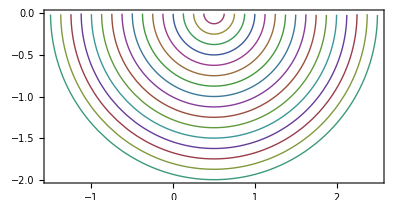

```mathematica
ParametricPlot[Evaluate[Table[cartesiancoordinates[refpoints][{ra,rb}],{rb,0,2,1/8}]],{ra,0,4},Frame->True]
```

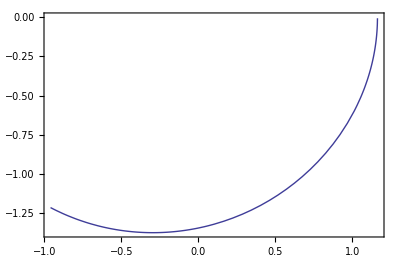

```mathematica
ParametricPlot[Evaluate[cartesiancoordinates[refpoints][{ra,rb}]/.{ra->1.3(1-r)+1.8r,rb->1.9(1-r)+.2r}],{r,0,1},Frame->True]
```

## How SVG and PDF formats draw curves: Cubic splines

If you dig through the reference manuals for 
Portable Data Format (PDF), http://www.adobe.com/devnet/acrobat/pdfs/PDF32000_2008.pdf ,
or Scalable Vector Graphics (SVG) http://www.w3.org/TR/SVG11/ ,
you'll find [PDF reference manual chapter 8.5.2.2. and SVG reference manual chapter 8.3.6 that a curved path is represented as a sequence of cubic Bézier splines.

A cubic Bézier spline is a curve that is described by 4 points  P_1, P_2, P_3, P_4
where P_1 and P_4 are the end points, and P_2 and P_3 are control points that define the tangent directions of the curve at the end points.

Here's an example:

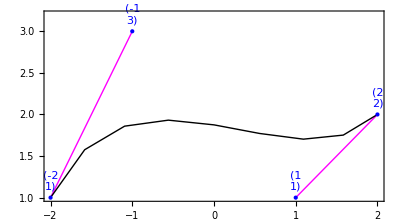

```mathematica
Graphics[{Magenta,Line/@Partition[#,2],Black,BezierCurve[#],Blue,Point[#],Text[MatrixForm[#],#+{0,.2}]&/@#},Frame->True,PlotRangePadding->0.2]&[{{-2,1},{-1,3},{1,1},{2,2}}]
```

The curve is defined by an equation

```mathematica
TraditionalForm[bezier3=P[1] s^3+3P[2] s^2 t+3P[3]s t^2+P[4] t^3/.s->1-t]
```

P(4) t^3+3 P(3) t^2 (1-t)+P(1) (1-t)^3+3 P(2) t (1-t)^2

where 0≤t≤1.

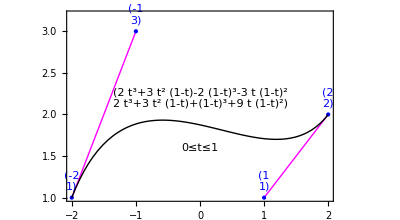

```mathematica
Show[Graphics[{Magenta,Line/@Partition[#,2],Black,Text[0≤t≤1,{0,1.6}],Text[MatrixForm[bezier3/.MapThread[Rule,{Array[P,4],#}]],{0,2.2}],Blue,Point[#],Text[MatrixForm[#],#+{0,.2}]&/@#},Frame->True,PlotRangePadding->0.2],ParametricPlot[bezier3/.MapThread[Rule,{Array[P,4],#}],{t,0,1},PlotStyle->Black]]&[{{-2,1},{-1,3},{1,1},{2,2}}]
```

### Cubic Bézier spline as sum of Bernstein polynomials

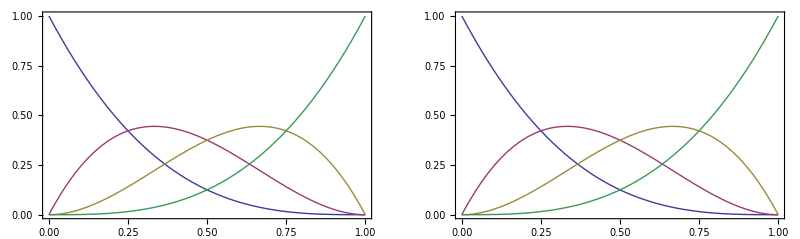

```mathematica
Show[GraphicsArray[{Plot[Evaluate[Table[BernsteinBasis[3,n,t],{n,0,3}]],{t,0,1},Frame->True],Plot[Evaluate[Table[Binomial[3,n](1-t)^(3-n)t^n,{n,0,3}]],{t,0,1},Frame->True]}]]
```

```mathematica
Sum[BernsteinBasis[3,n,t]P[n+1],{n,0,3}]
```

BernsteinBasis[3,0,t] P[1]+BernsteinBasis[3,1,t] P[2]+BernsteinBasis[3,2,t] P[3]+BernsteinBasis[3,3,t] P[4]

### Recurrence relation

```mathematica
recurrence={β[i_Integer,j_Integer/;j>0]->β[i,j-1](1-t0)+β[i+1,j-1]t0,β[i_Integer,0]->P[i+1]}
```

{β[i_Integer,j_Integer/;j>0]→(1-t0) β[i,-1+j]+t0 β[1+i,-1+j],β[i_Integer,0]→P[1+i]}

```mathematica
β[0,3]/.recurrence
%/.recurrence
%/.recurrence
%/.recurrence
```

(1-t0) β[0,2]+t0 β[1,2]

(1-t0) ((1-t0) β[0,1]+t0 β[1,1])+t0 ((1-t0) β[1,1]+t0 β[2,1])

(1-t0) ((1-t0) ((1-t0) β[0,0]+t0 β[1,0])+t0 ((1-t0) β[1,0]+t0 β[2,0]))+t0 ((1-t0) ((1-t0) β[1,0]+t0 β[2,0])+t0 ((1-t0) β[2,0]+t0 β[3,0]))

(1-t0) ((1-t0) ((1-t0) P[1]+t0 P[2])+t0 ((1-t0) P[2]+t0 P[3]))+t0 ((1-t0) ((1-t0) P[2]+t0 P[3])+t0 ((1-t0) P[3]+t0 P[4]))

```mathematica
β[0,3]//.recurrence/.(1-t0)->s0
Simplify[%]
TraditionalForm[%/.s0->1-t0]
```

s0 (s0 (s0 P[1]+t0 P[2])+t0 (s0 P[2]+t0 P[3]))+t0 (s0 (s0 P[2]+t0 P[3])+t0 (s0 P[3]+t0 P[4]))

s0^3 P[1]+3 s0^2 t0 P[2]+3 s0 t0^2 P[3]+t0^3 P[4]

P(4) t0^3+3 P(3) t0^2 (1-t0)+P(1) (1-t0)^3+3 P(2) t0 (1-t0)^2

## How cairo Draws Splines

Cairo http://cairographics.org is the graphics library used by inkscape.

Cairo uses the de Casteljau algorithm to split splines in half recursively until an approximation by a straight line differs by less than a defined error measure from the spline curve.

From http://cgit.freedesktop.org/cairo/tree/src/cairo-spline.c 
and http://cgit.freedesktop.org/cairo/tree/src/cairo-types-private.h :

### _cairo_spline_error_squared

This function computes a supremum of the maximal error made when approximating a cubic spline by a straight line

A spline is defined by 4 points {A,B,C,D}, corresponding to {P_1,P_2,P_3,P_4} in the computations above.

The following computation is performed:

Δ=D-A
β=B-A
β=Piecewise[{{β=B-A, if β·Δ≤0}, {β-Δ =B-D, if β·Δ≥Δ·Δ}, {β-(β·Δ)/(Δ·Δ)Δ, else}}]
ϵ_B=β·β
χ=C-A
χ=Piecewise[{{χ=C-A, if χ·Δ≤0}, {χ-Δ =C-D, if χ·Δ≥Δ·Δ}, {χ-(χ·Δ)/(Δ·Δ)Δ, else}}]
ϵ_C=χ·χ
ϵ=max{ϵ_B,ϵ_C}

i.e., the larger of the distances, squared, of the control points {B,C} (or {P_2,P_3} from the line OverBar[AD] (or OverBar[P_1 P_4]) is computed.

```mathematica
SplineErrorSquared=Function[{a,b,c,d},
Block[{Δ=d-a,β=b-a,χ=c-a},
Max[(#.#&[#-Which[#.Δ≤0,0,#.Δ≥Δ.Δ,Δ,True,(#.Δ)/(Δ.Δ)Δ]])&/@{β,χ}]
]
]
```

Function[{a,b,c,d},Block[{Δ=d-a,β=b-a,χ=c-a},Max[((#1.#1&)[#1-Which[#1.Δ≤0,0,#1.Δ≥Δ.Δ,Δ,True,(#1.Δ Δ)/(Δ.Δ)]]&)/@{β,χ}]]]

```mathematica
SplineErrorSquared[{-2,1},{-1,3},{1,1},{2,2}]
```

49/17

### _de_casteljau

The control points of two cubic splines covering the ranges 0≤t≤1/2 and 1/2≤t≤1 are computed from the arithmetic means of point pairs.

```mathematica
lerphalf[☺_,☹_]:=ToExpression[ToString[☺]<>ToString[☹]]->Mean[ToExpression/@{☺,☹}]
decasteljaurules=lerphalf@@#&/@{{a,b},{b,c},{c,d},{ab,bc},{bc,cd},{abbc,bccd}}
```

{ab→(a+b)/2,bc→(b+c)/2,cd→(c+d)/2,abbc→(ab+bc)/2,bccd→(bc+cd)/2,abbcbccd→(abbc+bccd)/2}

```mathematica
{{a,ab,abbc,abbcbccd},{abbcbccd,bccd,cd,d}}//.decasteljaurules
Simplify[%]
```

{{a,(a+b)/2,1/2 ((a+b)/2+(b+c)/2),1/2 (1/2 ((a+b)/2+(b+c)/2)+1/2 ((b+c)/2+(c+d)/2))},{1/2 (1/2 ((a+b)/2+(b+c)/2)+1/2 ((b+c)/2+(c+d)/2)),1/2 ((b+c)/2+(c+d)/2),(c+d)/2,d}}

{{a,(a+b)/2,1/4 (a+2 b+c),1/8 (a+3 b+3 c+d)},{1/8 (a+3 b+3 c+d),1/4 (b+2 c+d),(c+d)/2,d}}

```mathematica
deCasteljau=Function[{a,b,c,d},Evaluate[{{a,ab,abbc,abbcbccd},{abbcbccd,bccd,cd,d}}//.decasteljaurules]]
```

Function[{a,b,c,d},{{a,(a+b)/2,1/2 ((a+b)/2+(b+c)/2),1/2 (1/2 ((a+b)/2+(b+c)/2)+1/2 ((b+c)/2+(c+d)/2))},{1/2 (1/2 ((a+b)/2+(b+c)/2)+1/2 ((b+c)/2+(c+d)/2)),1/2 ((b+c)/2+(c+d)/2),(c+d)/2,d}}]

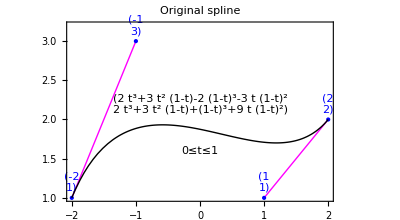

```mathematica
Show[Graphics[{Magenta,Line/@Partition[#,2],Black,Text[0≤t≤1,{0,1.6}],Text[MatrixForm[bezier3/.MapThread[Rule,{Array[P,4],#}]],{0,2.2}],Blue,PointSize[Medium],Point[#],Text[MatrixForm[#],#+{0,.2}]&/@#},Frame->True,PlotLabel->"Original spline",PlotRangePadding->0.2],ParametricPlot[bezier3/.MapThread[Rule,{Array[P,4],#}],{t,0,1},PlotStyle->Black]]&[{{-2,1},{-1,3},{1,1},{2,2}}]
```

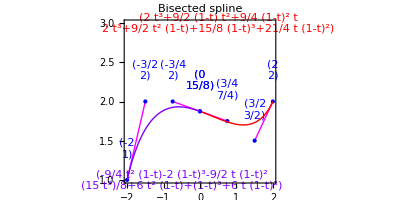

```mathematica
Show[MapIndexed[{Graphics[{Magenta,Line/@Partition[#,2],Hue[(#2⟦1⟧+2)/4],Text[MatrixForm[bezier3/.MapThread[Rule,{Array[P,4],#}]],{#-3/2,2#-1}&[#2⟦1⟧]],Blue,PointSize[Medium],Point[#],Text[MatrixForm[#],#+{0,.4}]&/@#},Frame->True,PlotLabel->"Bisected spline",PlotRangePadding->{0.2,0.6}],ParametricPlot[bezier3/.MapThread[Rule,{Array[P,4],#}],{t,0,1},PlotStyle->Hue[(#2⟦1⟧+2)/4]]}&,
deCasteljau[{-2,1},{-1,3},{1,1},{2,2}]
]
]
```

#### Sanity check: Verify that the splines are congruent

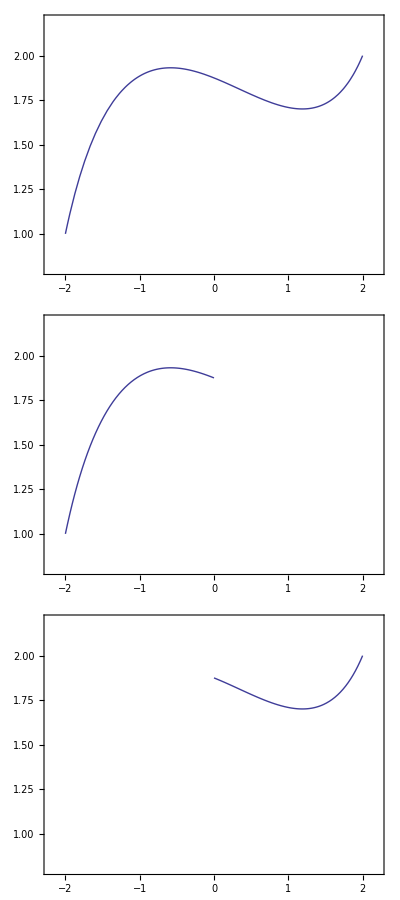

```mathematica
TableForm[ParametricPlot[Evaluate[bezier3/.MapThread[Rule,{Array[P,4],#}]],{t,0,1},Frame->True,PlotRange->{{-2.2,2.2},{0.8,2.2}}]&/@(Prepend[deCasteljau@@#,#]&[{{-2,1},{-1,3},{1,1},{2,2}}])]
```

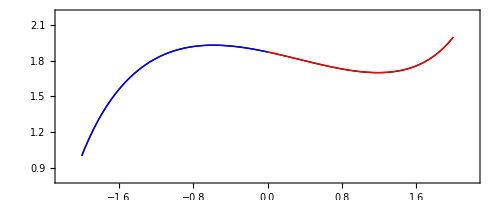

```mathematica
ParametricPlot[Evaluate[bezier3/.MapThread[Rule,{Array[P,4],#}]&/@(Prepend[deCasteljau@@#,#]&[{{-2,1},{-1,3},{1,1},{2,2}}])],{t,0,1},Frame->True,PlotRange->{{-2.2,2.2},{0.8,2.2}},PlotStyle->{Black,Blue,Red}]
```

#### Suprema of errors when approximated by straight line

```mathematica
N[√SplineErrorSquared[{-2,1},{-1,3},{1,1},{2,2}]]
N[√(SplineErrorSquared@@#)&/@deCasteljau[{-2,1},{-1,3},{1,1},{2,2}]]
```

1.69775

{0.715748,0.467837}

### _cairo_spline_decompose _cairo_spline_decompose_into

The object cairo_spline_t that describes a spline in cairo contains a component closure that is filled with a list of points.

If a spline can be approximated by a straight line to within a given tolerance, the first control point is added to the closure. Otherwise, the spline is split in two by the de Casteljau algorithm, and the decomposition algorithm is applied to both splines.

```mathematica
SplineDecomposeInto=Function[{controlpoints,tolerance},
If[SplineErrorSquared@@controlpoints<tolerance,
Point[First[controlpoints]],
SplineDecomposeInto[#,tolerance]&/@deCasteljau@@controlpoints]
]
```

Function[{controlpoints,tolerance},If[SplineErrorSquared@@controlpoints<tolerance,Point[First[controlpoints]],(SplineDecomposeInto[#1,tolerance]&)/@deCasteljau@@controlpoints]]

The last control point of the original control point set is added after recursively decomposing the spline.

```mathematica
SplineDecompose=Function[{controlpoints,tolerance},
Flatten[Append[SplineDecomposeInto[controlpoints,tolerance],Point[Last[controlpoints]]]]
]
```

Function[{controlpoints,tolerance},Flatten[Append[SplineDecomposeInto[controlpoints,tolerance],Point[Last[controlpoints]]]]]

#### Sanity check: Represent spline as set of points and as polyline

```mathematica
TableForm[SplineDecompose[{{-2,1},{-1,3},{1,1},{2,2}},.02]]
Line[%/.Point->Identity]
```

Point[{-2,1}]
Point[{-405/256,807/512}]
Point[{-35/32,119/64}]
Point[{0,15/8}]
Point[{35/32,109/64}]
Point[{405/256,897/512}]
Point[{2,2}]

Line[{{-2,1},{-405/256,807/512},{-35/32,119/64},{0,15/8},{35/32,109/64},{405/256,897/512},{2,2}}]

```mathematica
splineapprox=Function[{controlpoints,tolerance},List[Graphics[{Red,PointSize[Large],#,Blue,Line[#/.Point->Identity]}&[SplineDecompose[#,tolerance^2]],Frame->True,PlotLabel->"Spline approximated by line segments, Tolerance="<>ToString[tolerance]<>"^2",PlotRangePadding->0.2],ParametricPlot[bezier3/.MapThread[Rule,{Array[P,4],#}],{t,0,1},PlotStyle->Black]]&[controlpoints]];
```

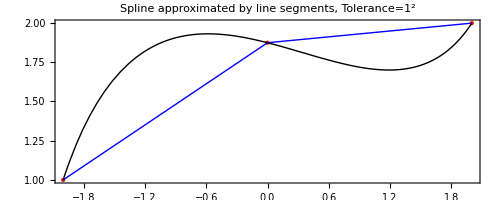

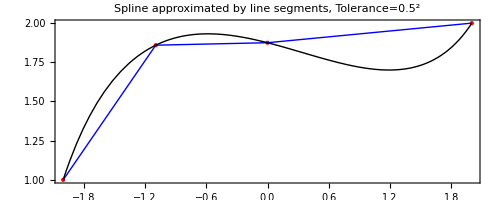

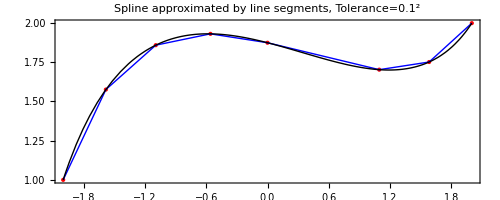

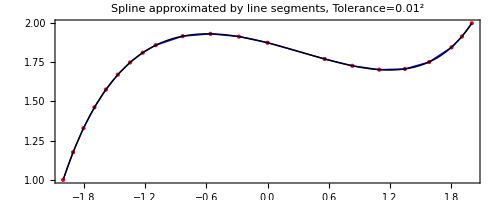

```mathematica
Print[Show[#]]&/@(splineapprox[{{-2,1},{-1,3},{1,1},{2,2}},#]&/@{1,0.5,0.1,.01});
```